# LTD Expression in Mathematica

```mathematica
Quit[]
```

## Setup

Import cLTD resources

```mathematica
Needs["cLTD`",NotebookDirectory[]<>"cLTD.m"];
FORMPATH="form";(*"<PASTE_HERE_YOUR_FULL_FORM_PATH_HERE_INSTEAD>"*)
SetOptions[cLTD,
	"WorkingDirectory"->"./",
	"FORMpath"->FORMPATH,
	"FORM_ID"->1];
SetOptions[GeneratecLTDExpression,
	"WorkingDirectory"->"./",
	"FORMpath"->FORMPATH,
	"FORM_ID"->1];
```

:::::::::::::::::::::::: cLTD ::::::::::::::::::::::::

Authors: Z. Capatti, V. Hirschi, D. Kermanschah, A. Pelloni, B. Ruijl

A Mathematica front end for cLTD [arxiv:2009.05509].

Import python resources

```mathematica
LTDsession=StartExternalSession[<|"System"->"Python","Version"->"3","ReturnType"->"String"|>];
ExternalEvaluate[LTDsession,"import sys; sys.path.insert(0,'"<>ToString[NotebookDirectory[]]<>"'); import ltd"];
```

Test it!

```mathematica
ToExpression[StringReplace[ExternalEvaluate[LTDsession,"ltd.get_cut_structures([(1, 0, 0), (0, 1, 0), (0, 0, 1), (1, -1, 0), (-1, 0, 1), (0, 1, -1)],['up','up','up'])"],"'"->""]]
```

{<|0→-1,1→-1,2→-1|>,<|0→-1,1→-1,4→-1|>,<|0→-1,1→-1,5→1|>,<|0→-1,2→-1,3→1|>,<|0→-1,2→-1,5→-1|>,<|0→-1,3→1,4→-1|>,<|0→-1,3→1,5→1|>,<|0→-1,4→-1,5→-1|>,<|1→-1,2→-1,3→-1|>,<|1→-1,2→-1,4→1|>,<|1→-1,3→-1,4→-1|>,<|1→-1,3→-1,5→1|>,<|1→-1,4→1,5→1|>,<|2→-1,3→1,4→1|>,<|2→-1,3→-1,5→-1|>,<|2→-1,4→1,5→-1|>}

Define wrapper

```mathematica
CallGetCutStructure[py3session_,signatures_, closures_, OptionsPattern[{DEBUG->False}]]:=Module[{strSig, strClosures,cmd, res},
strSig="[ "<>StringRiffle[Table["( "<>StringRiffle[Table[ToString[kiSig],{kiSig, propSig}], ", "]<>", )",{propSig ,signatures}],", "]<>" ]";
strClosures="[ "<>StringRiffle[Table["'"<>ToString[cl]<>"'",{cl,closures}],", "]<>" ]";
cmd = "ltd.get_cut_structures( "<>strSig<>", "<>strClosures<>" )";
If[OptionValue[DEBUG],Print["Calling Python with:\n"<>cmd];];
res=ExternalEvaluate[py3session,cmd];
If[OptionValue[DEBUG],Print["Python returned:\n"<>res];];
ToExpression[StringReplace[res,"'"->""]]
]
```

```mathematica
MakeAllExternalLegsIncoming[g_]:=Module[
{
OutgoingEdgesIndices
},
OutgoingEdgesIndices=Map[EdgeIndex[g,#⟦2⟧⟦1⟧]&,Select[Table[{iV,EdgeList[g,DirectedEdge[iV,_,___]|DirectedEdge[_,iV,___]]},{iV, VertexList[g]}],And[Length[#⟦2⟧]==1,EdgeCount[#⟦2⟧,DirectedEdge[_,#⟦1⟧,___]]==1]&]];
DirectedGraph[
Table[If[MemberQ[OutgoingEdgesIndices,ie],
EdgeList[g]⟦ie⟧/.{DirectedEdge[x_,y_,z___]:>DirectedEdge[y,x,z]},
EdgeList[g]⟦ie⟧
],{ie,Length[EdgeList[g]]}]
]
]
```

```mathematica
GetHalfEdges[g_]:=Module[{},
Flatten[Select[Table[EdgeList[g,DirectedEdge[iV,_,___]|DirectedEdge[_,iV,___]],{iV, VertexList[g]}],Length[#]==1&]]
]
```

```mathematica
RemoveHalfEdges[g_]:=Module[
{
HalfEdges
},
HalfEdges=GetHalfEdges[g];
DirectedGraph[Select[EdgeList[g],Not[MemberQ[HalfEdges,#]]&]]
]
```

```mathematica
RecursiveRemoveHalfEdges[g_]:=Module[
{
res
},
res=RemoveHalfEdges[g];
While[Length[GetHalfEdges[res]]>0,
res=RecursiveRemoveHalfEdges[res];
];
res
]
```

```mathematica
FindLMB[g_]:=Module[
{
loopUndirectedEdges,lmb,spanningTree
},
loopUndirectedEdges=Flatten[FindFundamentalCycles[UndirectedGraph[g]]];
spanningTree=EdgeList[FindSpanningTree[g]];
lmb=Select[
EdgeList[g],
And[Or[
MemberQ[loopUndirectedEdges,#/.{DirectedEdge[a_,b_,___]:>UndirectedEdge[a,b]}],
MemberQ[loopUndirectedEdges,#/.{DirectedEdge[a_,b_,___]:>UndirectedEdge[b,a]}]
],
Not[MemberQ[spanningTree,#/.{DirectedEdge[a_,b_,___]:>UndirectedEdge[a,b]}]],
Not[MemberQ[spanningTree,#/.{DirectedEdge[a_,b_,___]:>UndirectedEdge[b,a]}]]
]&
];
lmb
]
```

```mathematica
EdgeList[FindSpanningTree[myGraph]]//FullForm
```

EdgeList::graph: A graph object is expected at position 1 in EdgeList[FindSpanningTree[myGraph]].

EdgeList[FindSpanningTree[myGraph]]

```mathematica
RemoveExternalTrees[g_]:=Module[
{
loopUndirectedEdges,loopEdges, treeEdges
},
loopUndirectedEdges=Flatten[FindFundamentalCycles[UndirectedGraph[g]]];
loopEdges=Select[
EdgeList[g],
Or[
MemberQ[loopUndirectedEdges,#/.{DirectedEdge[a_,b_,___]:>UndirectedEdge[a,b]}],
MemberQ[loopUndirectedEdges,#/.{DirectedEdge[a_,b_,___]:>UndirectedEdge[b,a]}]
]&
];
treeEdges=Select[EdgeList[g],
Not[MemberQ[loopEdges,#]]&
];
DirectedGraph[
Join[loopEdges,Select[treeEdges,
Function[e,AnyTrue[
VertexList[DirectedGraph[loopEdges]]
,MatchQ[e,DirectedEdge[#,_,___]|DirectedEdge[_,#,___]]&]]
]]
]
]
```

```mathematica
RecursiveRemoveHalfEdges[g_]:=Module[
{
res
},
res=RemoveHalfEdges[g];
While[Length[GetHalfEdges[res]]>0,
res=RecursiveRemoveHalfEdges[res];
];
res
];
```

```mathematica
GetEdgeProperty[edge_,prop_]:=Module[{},
(edge/.{DirectedEdge[_,_,props_]:>props})[prop]
]
```

```mathematica
GetEdgeId[edge_]:=Module[{},
(edge/.{DirectedEdge[_,_,props_]:>props})["id"]
]
```

```mathematica
FindLMB[g_]:=Module[
{
loopUndirectedEdges,lmb,spanningTree
},
loopUndirectedEdges=Flatten[FindFundamentalCycles[UndirectedGraph[g]]];
spanningTree=EdgeList[FindSpanningTree[g]];
lmb=Select[
EdgeList[g],
And[Or[
MemberQ[loopUndirectedEdges,#/.{DirectedEdge[a_,b_,___]:>UndirectedEdge[a,b]}],
MemberQ[loopUndirectedEdges,#/.{DirectedEdge[a_,b_,___]:>UndirectedEdge[b,a]}]
],
Not[MemberQ[spanningTree,#/.{DirectedEdge[a_,b_,___]:>DirectedEdge[a,b]}]]
]&
];
lmb
]
```

```mathematica
ShowGraph[g_, OptionsPattern[{size->500, showDetails->True}]]:=Module[{},

DirectedGraph[EdgeList[g],
VertexLabels->Automatic,
EdgeLabels->Table[e->(e/.(DirectedEdge[_,_,p___]:>
StringRiffle[ToString[#,StandardForm]&/@Join[
{Style[ToString[p["id"]],FontSize->15,Blue]},
If[OptionValue[showDetails],{Style[p["mass"],FontSize->12,Black]},{}],
If[OptionValue[showDetails],{Style[p["sig"],FontSize->10,Black]},{}]
]," | "]
)),{e,EdgeList[g]}],
ImageSize->OptionValue[size]]

]
```

```mathematica
ComputeCutStructure[py3session_,g_, OptionsPattern[{closures->Automatic, DEBUG->False}]]:=Module[{sigs,loopEdges,cl, cutStructure},

loopEdges=Select[EdgeList[g],Not[AllTrue[GetEdgeProperty[#,"sig"]⟦1⟧,Function[s,s==0]]]&];
sigs = Table[GetEdgeProperty[e,"sig"]⟦1⟧,{e,loopEdges}];
If[OptionValue[closures]===Automatic,
cl = Table["up",{i,Length[sigs⟦1⟧]}];,
cl = OptionValue[closures];
];
cutStructure = CallGetCutStructure[py3session,sigs,cl, DEBUG->OptionValue[DEBUG]];

Table[
Association[
Table[
GetEdgeId[loopEdges⟦edgeIndex+1⟧]->csElem[edgeIndex]
,{edgeIndex,Keys[csElem]}]
],
{csElem,cutStructure}]

]
```

## Examples

A simple triangle graph

```mathematica
myGraph = DirectedGraph[
{
(* The third entry 'i' in DirectedEdge[x,y,i] is your chosen label ID for that edge, you can also leave it off if you just want sequential labels *)
DirectedEdge[1,2,11],
DirectedEdge[2,3,12],
DirectedEdge[3,1, 13],
DirectedEdge[101,1, 101],
DirectedEdge[102,2, 102],
DirectedEdge[103,3,103]
}
];
```

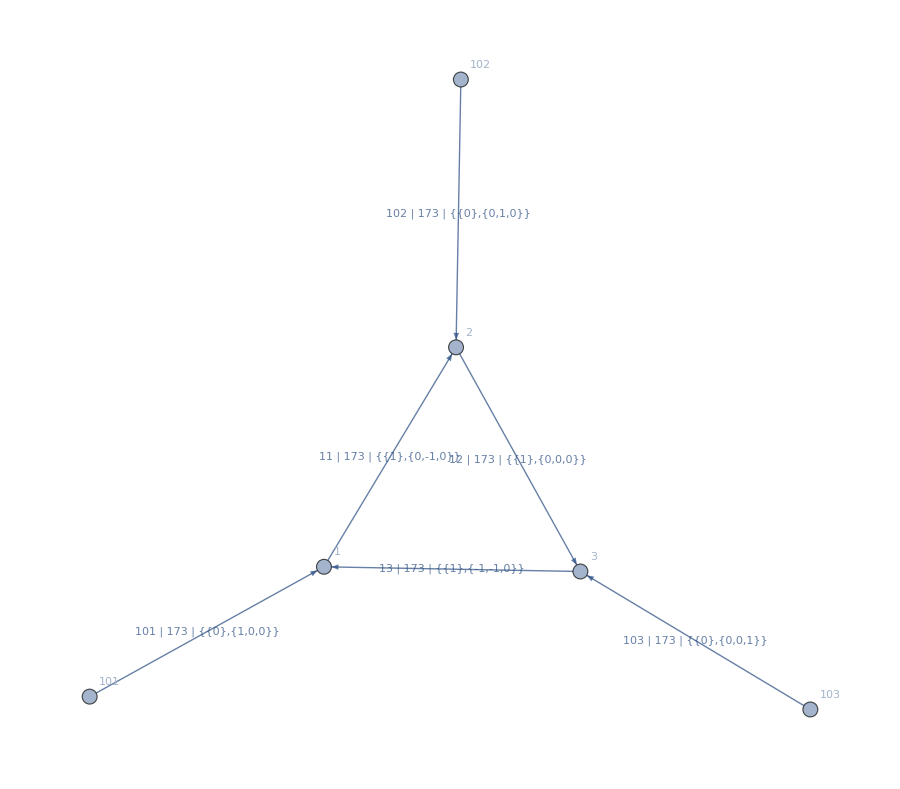

```mathematica
myDressedGraph=AssignSignatures[myGraph,
masses->Association[Table[(e/.{DirectedEdge[_,_,id_]:>id})->173,{e,EdgeList[myGraph]}]],
lmb-> {12}
];
ShowGraph[myDressedGraph, size->900]
```

```mathematica
ComputeCutStructure[LTDsession, myDressedGraph, DEBUG->False, closures->{"up"}]
ComputeCutStructure[LTDsession, myDressedGraph, DEBUG->False, closures->{"down"}]
```

{<|11→-1|>,<|12→-1|>,<|13→-1|>}

{<|11→1|>,<|12→1|>,<|13→1|>}

Now a four-loop ladder

```mathematica
myGraph = DirectedGraph[
{
(* The third entry 'i' in DirectedEdge[x,y,i] is your chosen label ID for that edge, you can also leave it off if you just want sequential labels *)
DirectedEdge[1,2,1],
DirectedEdge[2,3,2],
DirectedEdge[3,4,3],
DirectedEdge[4,5,4],

DirectedEdge[11,22,11],
DirectedEdge[22,33,12],
DirectedEdge[33,44,13],
DirectedEdge[44,55,14],

DirectedEdge[1,11,21],
DirectedEdge[2,22,22],
DirectedEdge[3,33,23],
DirectedEdge[4,44,24],
DirectedEdge[5,55,25],

DirectedEdge[101,1,  101],
DirectedEdge[102,11,102],
DirectedEdge[103,5,  104],
DirectedEdge[104,55,103]

}
];
```

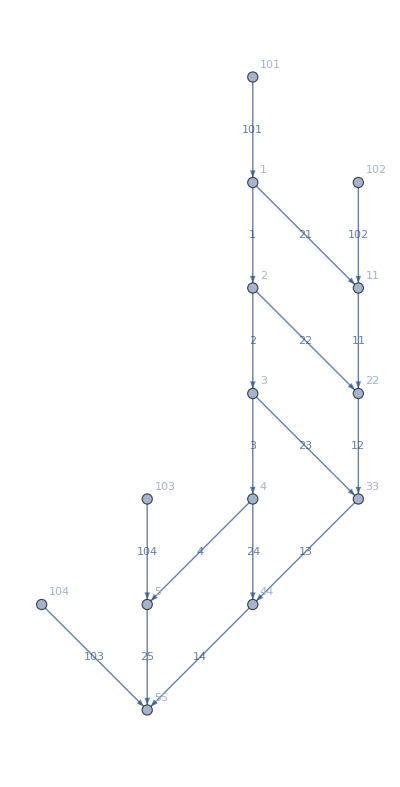

```mathematica
myDressedGraph=AssignSignatures[myGraph,
masses->Association[Table[(e/.{DirectedEdge[_,_,id_]:>id})->173,{e,EdgeList[myGraph]}]],
lmb-> {1,2,3,4}
];
ShowGraph[myDressedGraph, size->400, showDetails->False]
```

```mathematica
ComputeCutStructure[LTDsession, myDressedGraph, DEBUG->False]⟦1⟧
ComputeCutStructure[LTDsession, myDressedGraph, DEBUG->False, closures->{"down","up","up","up"}]⟦1⟧
```

<|1→-1,2→-1,3→-1,4→-1|>

<|1→1,2→-1,3→-1,4→-1|>

Now a random graph :)

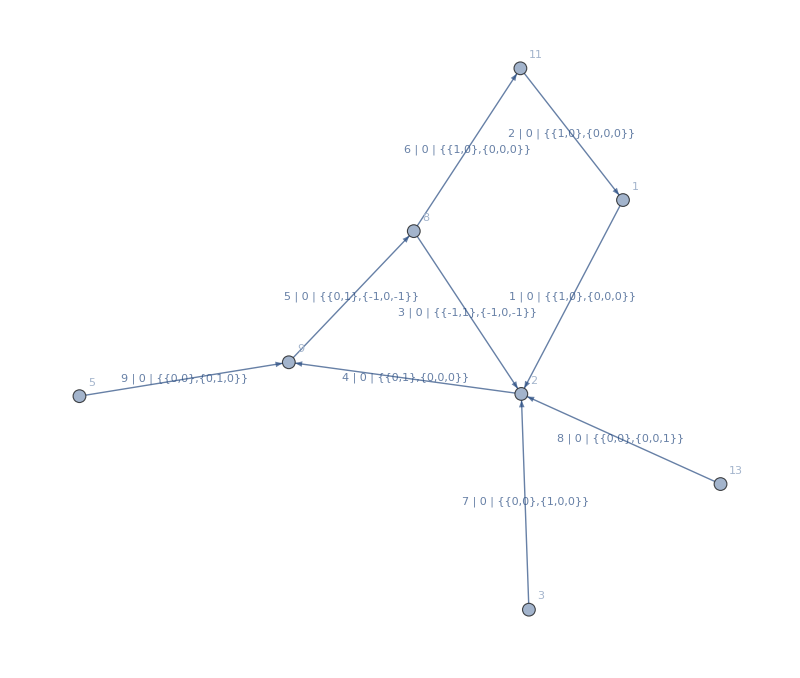

11

```mathematica
SeedRandom[10];myGraph=MakeAllExternalLegsIncoming[RemoveExternalTrees[DirectedGraph[EdgeList[RandomGraph[{13,13}]],"Random"]]];
myDressedGraph=AssignSignatures[myGraph,
masses->Association[Table[(e/.{DirectedEdge[_,_,id_]:>id})->173,{e,EdgeList[myGraph]}]],
lmb->  Table[Position[EdgeList[myGraph],e]⟦1⟧⟦1⟧,{e,FindLMB[myGraph]}]
];
ShowGraph[myDressedGraph, size->800, showDetails->True]
ComputeCutStructure[LTDsession, myDressedGraph,DEBUG->False]//Length
```